## Definiciones

## Operadores

### Coin

```mathematica
-Graphics-;
```

```mathematica
n[α_,ϕ_]:={Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}
```

```mathematica
Paulis=PauliMatrix/@Range[3];
```

```mathematica
expCoin[θ_,α_,ϕ_]:=MatrixExp[(-ⅈ θ)/2(n[α,ϕ].Paulis)]
```

```mathematica
Coin[θ_,α_,ϕ_,t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[expCoin[θ,α,ϕ]]]
```

```mathematica
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
Coin[θ,α,ϕ,t]
```

SparseArray[…]

### Shift

```mathematica
Shift[t_Integer]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
```

```mathematica
t=1;
Shift[t].{0,0,1,0,0,0}
```

{0.,0.,0.,0.,1.,0.}

### Unitaria

```mathematica
Unitary[θ_,α_,ϕ_,t_Integer]:=Shift[t].Coin[θ,α,ϕ,t]
```

```mathematica
θ=0.52π;
α=0.23π;
ϕ=1.75π;
Unitary[θ,α,ϕ,2].ArrayPad[Unitary[θ,α,ϕ,1].{0,0,1,0,0,0},2]//FullSimplify//Chop
```

{0,-0.0469526-0.419743 ⅈ,0,0,-0.232397,-0.419743-0.0469526 ⅈ,0,0,0.169606-0.748631 ⅈ,0}

```mathematica
Unitary[paramsCoin_List,t_Integer]:=Module[{coinProduct},
coinProduct=Dot@@(Coin[##,t]&@@@Reverse[paramsCoin]);
Shift[t].coinProduct]
```

```mathematica
θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;

Unitary[params,t]//Normal
Shift[t].Dot@@(Coin[##,t]&@@@Reverse[{{θ1,α1,ϕ1},{θ2,α2,ϕ2}}])//Normal
Shift[t].Coin[θ2,α2,ϕ2,t].Coin[θ1,α1,ϕ1,t]//Normal
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0.293893 ⅈ,-0.951057+0.0954915 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.951057-0.0954915 ⅈ,0.+0.293893 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

## Funciones cálculos

### Estados de la moneda

```mathematica
state0={1.,0.};
state1={0.,1.};
plusX=1/Sqrt[2]{1.,1.};
minusX=1/Sqrt[2]{1.,-1.};
plusY=1/Sqrt[2.]{1,ⅈ};
minusY=1/Sqrt[2.]{1,-ⅈ};
```

```mathematica
HVecs=N[Normalize/@Eigenvectors[HadamardMatrix[2]]];
HMinus=HVecs[[1]];
HPlus=HVecs[[2]];
```

### Hallar antípoda

```mathematica
FindAntipode[polar_,azimutal_]:=Module[{newPolar,newAzimutal},
{newPolar=π-polar,
newAzimutal=azimutal+π}
]
```

```mathematica
α=6π/10;
ϕ=0;
FindAntipode[α,ϕ]
```

{(2 π)/5,π}

### Estado final de la caminata después de t pasos

```mathematica
DQWL[coin0_,θ_,α_,ϕ_,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[θ,α,ϕ,i]],{i,t}];
psi
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
DQWL[coin0,θ,α,ϕ,t]
```

{0,-0.672499+0.275336 ⅈ,0,0,-0.672499+0.140291 ⅈ,0}

```mathematica
DQWL[coin0_,paramsCoin_List,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[paramsCoin,i]],{i,t}];
psi
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};

θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;
DQWL[coin0,params,t]
```

{0,-0.672499+0.275336 ⅈ,0,0,-0.672499+0.140291 ⅈ,0}

### Distribución de probabilidad

```mathematica
PosProbDistrib[psi_,tmax_]:=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2(2tmax+1),2]]
```

```mathematica
coin0=state0;
θ=0.52π;
α=0.23π;
ϕ=1.75π;
t=3;
PosProbDistrib[DQWL[coin0,θ,α,ϕ,t],t]
```

{0.136932,0,0.108026,0,0.302759,0,0.452283}

### Distribución de probabilidad para cada uno de los pasos

```mathematica
PosProbDisTime[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@θ,N@α,N@ϕ,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
P1=PosProbDisTime[coin0,θ,α,ϕ,t]
```

{{0,1.,0},{0.528064,0,0.471936}}

```mathematica
PosProbDisTime[coin0_,paramsCoin_List,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@paramsCoin,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};

θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;
P2=PosProbDisTime[coin0,params,t]
```

{{0,1.,0},{0.528064,0,0.471936}}

### Valor de expectación

```mathematica
ExpecValue[posProbDisTime_List, t_Integer]:=Flatten[Chop[posProbDisTime.Range[-t,t]]]
```

```mathematica
t=1;
ExpV=ExpecValue[P2, t]
```

{0,-0.0561285}

### Determinar si la estrategia es ganadora o perdedora

```mathematica
WinningQ[expValsList_List] := 
  Which[
SameQ@@expValsList,"Indefinido",
    OrderedQ[expValsList], "Ganadora",
    OrderedQ[expValsList, GreaterEqual], "Perdedora",
    True, "No se puede determinar"
  ]
```

```mathematica
WinningQ[EV]
```

WinningQ[EV]

### Calcular posProbDistTime, expval y typeStrategy

```mathematica
CalculateData[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,θ,α,ϕ,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;

CalculateData[coin0,θ,α,ϕ,t]
```

{{{0,1.,0},{0.528064,0,0.471936}},{0,-0.0561285},Perdedora}

```mathematica
CalculateData[coin0_,paramsCoin_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,paramsCoin,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};

θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;
CalculateData[coin0,params,t]
```

{{{0,1.,0},{0.528064,0,0.471936}},{0,-0.0561285},Perdedora}

### Fijar θ y α, variar ϕ

```mathematica
VaryingPhi[coin0_,θ_,α_,nϕ_Integer,t_Integer]:=Module[{ϕ},
Table[
Flatten[{ϕ=i *2π/nϕ,
CalculateData[coin0,θ,α,ϕ,t]},
1],
{i,0,nϕ-1}
]
]
```

```mathematica
coin0=plusX;
θ=9π/5;
α=2 π/5;
nϕ=2;
t=1;
A=VaryingPhi[coin0,θ,α,nϕ,t]
```

{{0,{{0,1.,0},{0.471936,0,0.528064}},{0,0.0561285},Ganadora},{π,{{0,1.,0},{0.528064,0,0.471936}},{0,-0.0561285},Perdedora}}

### Fijar θ , variar α y ϕ

```mathematica
VaryingAlpha[coin0_,θ_,nα_Integer,nϕ_Integer,t_Integer]:=Module[{α},
Flatten[
Table[α=j*Pi/(nα-1);
Map[Prepend[#,α]&,
VaryingPhi[coin0,θ,α,nϕ,t]
],
{j,0,nα-1}],
1]
]
```

```mathematica
coin0=plusX;
θ=9π/5;
nα=2;
nϕ=2;
t=1;
B=VaryingAlpha[coin0,θ,nα,nϕ,t]
```

{{0,0,{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido},{0,π,{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido},{π,0,{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido},{π,π,{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}}

### Variar θ, α y ϕ

```mathematica
VaryingTheta[psi0_,nθ_Integer,nα_Integer,nϕ_Integer,t_Integer]:=Module[{θ},
Flatten[Table[θ=k*2*Pi/nθ;
Map[Prepend[#,θ]&,
VaryingAlpha[psi0,θ,nα,nϕ,t]
],
{k,0,nθ-1}],
1]
]
```

```mathematica
coin0=minusX;
nθ=2;
nα=3;
nϕ=4;
t=10;
F=VaryingTheta[coin0,nθ,nα,nϕ,t];
```

### Extract data for FixedTimeExpValPlot

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2]]
```

{d,e,f}

```mathematica
#[[2]]&/@{{a,b,c},{d,e,f},{g,h,i}}
```

{b,e,h}

```mathematica
Flatten[{#[[2;;3]],#[[5,-1]]}]&/@F
```

{{0,0,0},{0,π/2,0},{0,π,0},{0,(3 π)/2,0},{π/2,0,0},{π/2,π/2,0},{π/2,π,0},{π/2,(3 π)/2,0},{π,0,0},{π,π/2,0},{π,π,0},{π,(3 π)/2,0},{0,0,0},{0,π/2,0},{0,π,0},{0,(3 π)/2,0},{π/2,0,0},{π/2,π/2,0},{π/2,π,0},{π/2,(3 π)/2,0},{π,0,0},{π,π/2,0},{π,π,0},{π,(3 π)/2,0}}

```mathematica
ExtractDataExpVal[varyingAlpha_List,t_Integer]:=Flatten[{#[[1;;2]],#[[4,t+1]]}]&/@varyingAlpha
```

```mathematica
ExtractDataExpVal[B,1]
```

{{0,0,0},{0,π,0},{π,0,0},{π,π,0}}

### Extract data for SphereGraph

```mathematica
Flatten[{#[[2;;3]],#[[6]]}]&/@F
```

{{0,0,Indefinido},{0,π/2,Indefinido},{0,π,Indefinido},{0,(3 π)/2,Indefinido},{π/2,0,Indefinido},{π/2,π/2,Indefinido},{π/2,π,Indefinido},{π/2,(3 π)/2,Indefinido},{π,0,Indefinido},{π,π/2,Indefinido},{π,π,Indefinido},{π,(3 π)/2,Indefinido},{0,0,Indefinido},{0,π/2,Indefinido},{0,π,Indefinido},{0,(3 π)/2,Indefinido},{π/2,0,Indefinido},{π/2,π/2,Indefinido},{π/2,π,Indefinido},{π/2,(3 π)/2,Indefinido},{π,0,Indefinido},{π,π/2,Indefinido},{π,π,Indefinido},{π,(3 π)/2,Indefinido}}

```mathematica
ExtractDataSphereGraph[varyingAlpha_List]:=Flatten[{#[[1;;2]],#[[5]]}]&/@varyingAlpha
```

```mathematica
ExtractDataSphereGraph[B]
```

{{0,0,Indefinido},{0,π,Indefinido},{π,0,Indefinido},{π,π,Indefinido}}

## Funciones gráficas

#### Colores

```mathematica
Midnight=RGBColor["#311441"];
Sky=RGBColor["#35A3FA"];
AcuaGreen=RGBColor["#47F884"];
DirtyYellow=RGBColor["#E1DC46"];
HotOrange=RGBColor["#F4651D"];
Wine=RGBColor["#7D0402"];
ArticleColors=(Blend[{Midnight,Sky,AcuaGreen,DirtyYellow,HotOrange,Wine},#]&);
```

```mathematica
SphereColor=RGBColor["#DFF7FF"];
```

```mathematica
CH1=RGBColor["#9C0147"];
CH2=RGBColor["#DC0014"];
CH3=RGBColor["#FA742C"];
CH4=RGBColor["#FFB33C"];
CH5=RGBColor["#FFE04D"];
CC1=RGBColor["#80B83"];
CC2=RGBColor["#1E9B9D"];
CC3=RGBColor["#0472BD"];
CC4=RGBColor["#063DAC"];
CC5=RGBColor["#2C139B"];
```

#### Label coin

```mathematica
LabelCoinState[state0]:="0";
LabelCoinState[state1]:="1";
LabelCoinState[plusX]:="+_x"
LabelCoinState[minusX]:="-_x"
LabelCoinState[plusY]:="-_y"
LabelCoinState[minusY]:="-_y"
LabelCoinState[HMinus]:="H_-"
LabelCoinState[HPlus]:="H_+"
```

#### Probabilidad respecto al tiempo

```mathematica
PosProbDisTimePlot[posProbDisTime_List,opts:OptionsPattern[ArrayPlot]]:=
ArrayPlot[posProbDisTime,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
DataReversed->True,
ColorFunction->ArticleColors,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicks->{{Table[{i,i-1,0},{i,1,(2t+1-1)/2+1,(2t+1-1)/12}],None},{Table[{i,i-1-t,0},{i,1,2t+1,t}],None}},
FrameTicksStyle->13,
PlotRangePadding->0,
PlotLegends->BarLegend[
Automatic,
LegendLabel->""
]
]
```

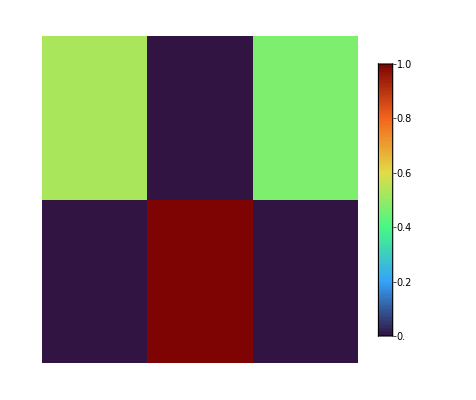

```mathematica
PosProbDisTimePlot[P2]
```

#### Valor de expectación respecto al tiempo

```mathematica
Clear@ExpValVsTimePlot
```

```mathematica
ExpValVsTimePlot[expecValue_List,t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],expecValue}ᵀ,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
Mesh->All,
PlotStyle->Thickness[0.005],
GridLines->{Range[Automatic,Automatic,50],Range[Automatic,Automatic,20]},
GridLinesStyle->Thin,
Evaluate@opts
]
```

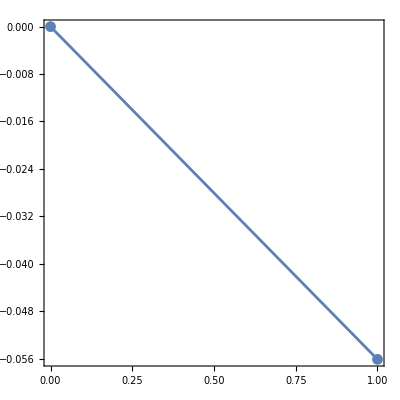

```mathematica
ExpValVsTimePlot[ExpV,1]
```

```mathematica
ExpValVsTimePlot[{expecValues__List},t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],#}ᵀ&/@{expecValues},
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
PlotStyle->Thickness[0.005],
Mesh->All,
Evaluate@opts
]
```

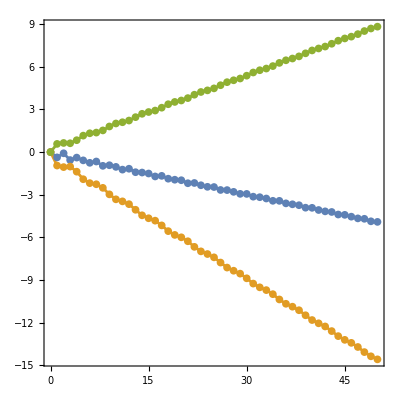

```mathematica
coin0=plusX;

θ1=π;
α1=0.39π;
ϕ1=1.3π;

θ2=3π/2;
α2=0.39π;
ϕ2=1.3π;

t=50;

G=CalculateData[coin0,θ1,α1,ϕ1,t];
H=CalculateData[coin0,θ2,α2,ϕ2,t];
J=CalculateData[coin0,{{θ1,α1,ϕ1},{θ2,α2,ϕ2}},t];

ExpValVsTimePlot[{G[[2]],H[[2]],J[[2]]},t,PlotLegends->{"","",""}]
```

#### Valor de expectación para un tiempo fijo

```mathematica
ClearAll@FixedTimeExpValPlot
```

```mathematica
FixedTimeExpValPlot[data_List,fixedt_Integer,initCoinState_,θ_,nα_Integer,nϕ_Integer,opts:OptionsPattern[ListDensityPlot]]:=Module[{alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{2*i π/nα,ToString[TraditionalForm[2*i π/nα]]},{i,0,nα}];
phiTicks=Table[{2*i*2π/nϕ,ToString[TraditionalForm[2*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{ColorData[{"Rainbow",{-10,10}}][#]&,{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],"     θ = ",θ,",     = ",fixedt}]]]
```

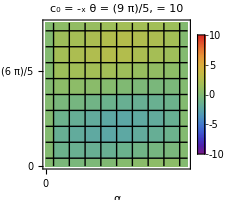

```mathematica
coin0=minusX;
θ=9π/5;
nα=10;
nϕ=10;
t=10;
fixedt=10;
res=VaryingAlpha[coin0,θ,nα,nϕ,t];
data=ExtractDataExpVal[res,fixedt];
FixedTimeExpValPlot[data,fixedt,coin0,θ,nα,nϕ]
```

#### Marcar el punto en la esfera de Bloch

```mathematica
PolarPoint[{r_,polar_,azimutal_}]:=Point[r*{Sin[polar] Cos[azimutal],Sin[polar] Sin[azimutal],Cos[polar]}]
```

```mathematica
ClearAll@SphereGraph
```

```mathematica
SphereGraph[data_List,initCoinState_,θ_,opts:OptionsPattern[Graphics3D]]:=Module[{sphere},
sphere=Graphics3D[{
Opacity[0.95],Glow[SphereColor],Black,Sphere[],
Opacity[1],PointSize[0.03],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,1.2}}],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{-1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,-1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,-1.2}}],

Text[Style["",14,Black],{1.3,0,0}],
Text[Style["",14,Black],{0,1.3,0}],
Text[Style["",14,Black],{0,0,1.3}],

RGBColor["#00D52C"],Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Ganadora"&]}],
Red,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Perdedora"&]}],
Black,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Indefinido"&]}],
Gray,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="No se puede determinar"&]}]
},
Boxed->False,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],",    θ = ",θ}]
]
]
```

```mathematica
coin0=minusX;
θ=9π/5;
nα=10;
nϕ=10;
t=10;
res=VaryingAlpha[coin0,θ,nα,nϕ,t];
data=ExtractDataSphereGraph[res];
SphereGraph[data,coin0,θ]
```

-Graphics3D-

## Estado inicial 0para la moneda

## Estado inicial -_xpara la moneda

```mathematica
coin0=minusX;
nθ=10;
nα=10;
nϕ=10;
t=10;
r0=VaryingTheta[coin0,nθ,nα,nϕ,t];
```

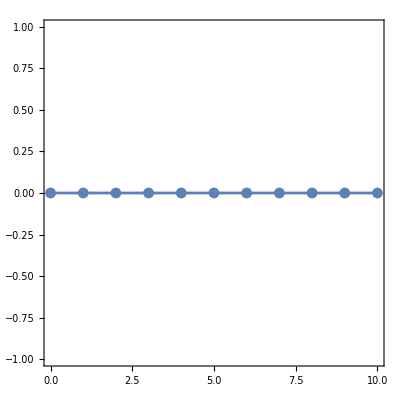

```mathematica
θi=1;
nθ=10;
t=10;
probs=r0[[(θi-1)*nθ*nα+1;;θi*nθ*nα,4]];
ExpValVsTimePlot[ExpecValue[probs[[θi]],t],t]
```

```mathematica
Table[data=ExtractDataSphereGraph[r0[[(i-1)*nθ*nα+1;;i*nθ*nα,2;;]]];
SphereGraph[data,coin0,(i-1)*2π/nθ],
{i,1,nθ}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

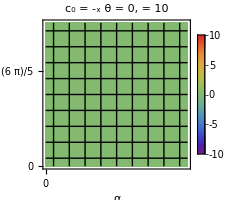
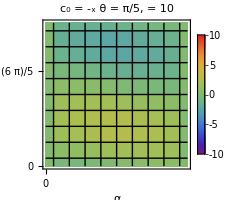
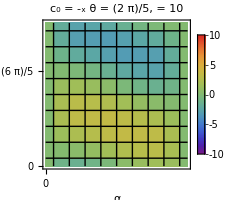
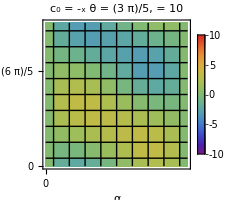
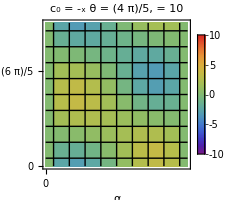
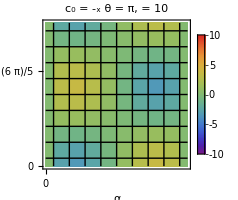
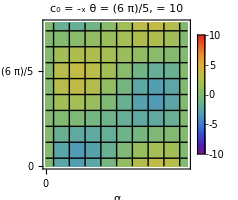
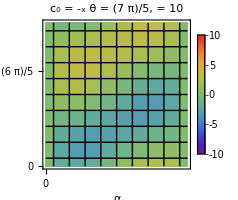
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fixedt=10;
Table[data=ExtractDataExpVal[r0[[(i-1)*nθ*nα+1;;i*nθ*nα,2;;]],fixedt];
FixedTimeExpValPlot[data,fixedt,coin0,(i-1)*2π/nθ,nα,nϕ],
{i,1,nθ}
]
```

## Pruebas

```mathematica
coin0=state0;
θ=π;
α=π/2;
ϕ=π;
t=5;
R=CalculateData[coin0,θ,α,ϕ,t]
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,1./√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |+_x⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
state0
```

{1.,0.}

```mathematica
coin0=state0;
θ=π;
α=π/2;
ϕ=π;
t=100;
R=CalculateData[coin0,θ,α,ϕ,t];
```

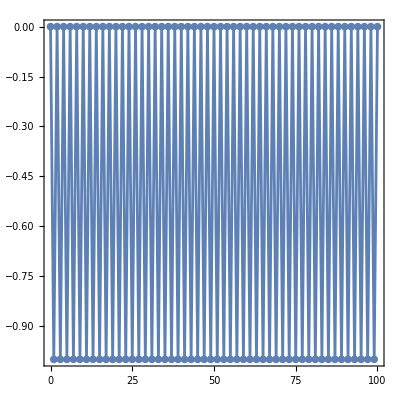

```mathematica
ExpValVsTimePlot[R[[2]]]
```

### Paradoja 1

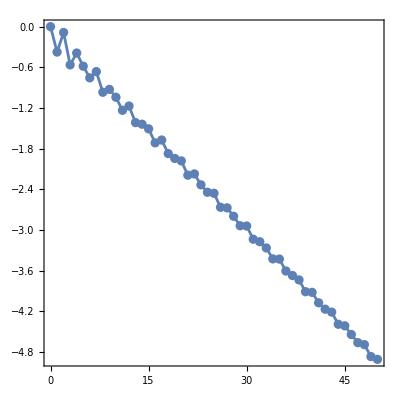

```mathematica
coin0=plusX;
θ=π;
α=0.39π;
ϕ=1.3π;
t=50;
R1=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R1[[2]]]
```

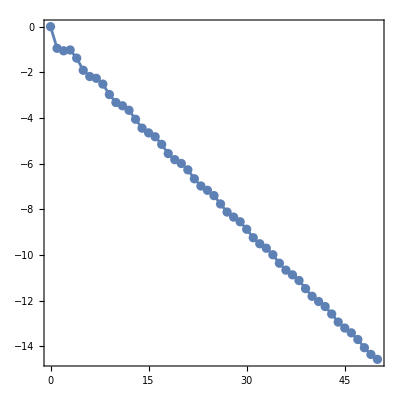

```mathematica
coin0=plusX;
θ=3π/2;
α=0.39π;
ϕ=1.3π;
t=50;
R2=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R2[[2]]]
```

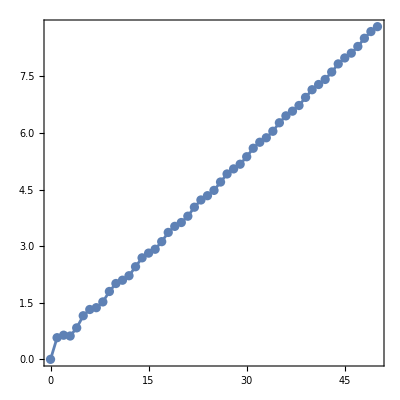

```mathematica
coin0=plusX;
θ=π+3π/2;
α=0.39π;
ϕ=1.3π;
t=50;
R3=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R3[[2]]]
```

```mathematica
coin0=plusX;

θ1=π;
α1=0.39π;
ϕ1=1.3π;

θ2=3π/2;
α2=0.39π;
ϕ2=1.3π;

t=50;

R4=CalculateData[coin0,{{θ1,α1,ϕ1},{θ2,α2,ϕ2}},t];

ExpValVsTimePlot[R4[[2]]]
```

-Graphics-

### Paradoja 2

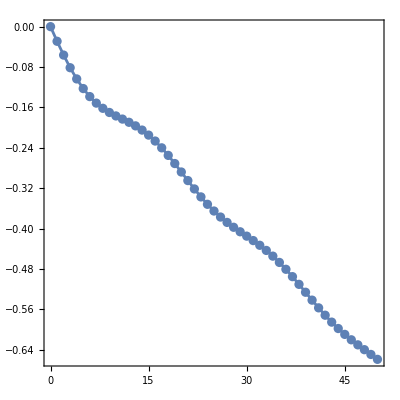

```mathematica
coin0=plusX;
θ=π/8;
α=0.33π;
ϕ=0.06π;
t=50;
R5=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R5[[2]]]
```

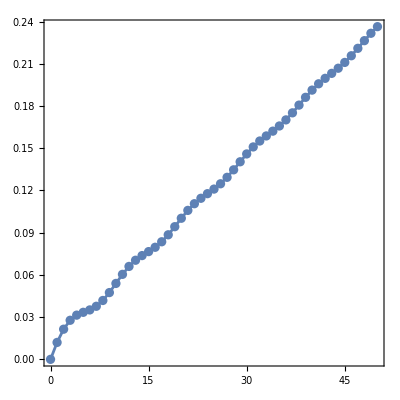

```mathematica
coin0=plusX;
θ=2(π/8);
α=0.33π;
ϕ=0.06π;
t=50;
R6=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R6[[2]]]
```

```mathematica
coin0=plusX;

θ1=π/8;
α1=0.33π;
ϕ1=0.06π;

θ2=π/8;
α2=0.33π;
ϕ2=0.06π;

t=50;

R7=CalculateData[coin0,{{θ1,α1,ϕ1},{θ2,α2,ϕ2}},t];

ExpValVsTimePlot[R7[[2]]]
```

-Graphics-

```mathematica
θ=.;
α=.;
ϕ=.;
expCoin[θ,α,ϕ]//FullSimplify//MatrixForm
```

(Cos[θ/2]-ⅈ Cos[α] Sin[θ/2] | Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]-Sin[ϕ])
Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]+Sin[ϕ]) | Cos[θ/2]+ⅈ Cos[α] Sin[θ/2])

### Paradoja 1

```mathematica
coin0=plusX;
θ=π;
α=0.39π;
ϕ=1.3π;
t=50;
R1=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R1[[2]]]
```

-Graphics-

```mathematica
coin0=plusX;
θ=3π/2;
α=0.39π;
ϕ=1.3π;
t=50;
R2=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R2[[2]]]
```

-Graphics-

```mathematica
coin0=plusX;
θ=π+3π/2;
α=0.39π;
ϕ=1.3π;
t=50;
R3=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R3[[2]]]
```

-Graphics-

```mathematica
coin0=plusX;

θ1=π;
α1=0.39π;
ϕ1=1.3π;

θ2=3π/2;
α2=0.39π;
ϕ2=1.3π;

t=50;

R4=CalculateData[coin0,{{θ1,α1,ϕ1},{θ2,α2,ϕ2}},t];

ExpValVsTimePlot[R4[[2]]]
```

-Graphics-